```mathematica
Clear["Global`*"]
α[α1_,α2_,θ1_,θ2_]:=If[Sin[α1+α2]^2-4 Sin[α1]Sin[α2] Sin[θ1-θ2]^2(Cos[α1+α2]+Sin[α1]Sin[α2] Sin[θ1-θ2]^2)==0,0,If[θ1==θ2,α1+α2,ArcTan[Cos[α1] Cos[α2]-Sin[α1] Sin[α2]Cos[2 (θ1-θ2)],(Sin[α1+α2]^2-4 Sin[α1]Sin[α2] Sin[θ1-θ2]^2(Cos[α1+α2]+Sin[α1]Sin[α2] Sin[θ1-θ2]^2))^(1/2)]]];
θ[α1_,α2_,θ1_,θ2_]:=If[α[α1,α2,θ1,θ2]==0,0,If[θ1==θ2,θ1,1/2 ArcTan[Sin[α1] Cos[α2]Cos[2θ1]+Cos[α1] Sin[α2]Cos[2 θ2],(Sin[α1]^2 Sin[α2]^2 Sin[2(θ1-θ2)]^2+(Sin[α1] Cos[α2]Sin[2θ1]+Cos[α1] Sin[α2]Sin[2 θ2])^2)^(1/2)]]];
ϕ[α1_,α2_,θ1_,θ2_]:=If[θ[α1,α2,θ1,θ2]==0 ∨ θ1==θ2,0,-ArcTan[Sin[α1] Cos[α2]Sin[2θ1]+Cos[α1] Sin[α2]Sin[2 θ2],Sin[α1] Sin[α2]Sin[2 (θ1-θ2)]]];
g[ω_,ω1_,m_,F_,α_]:=π/F 1/(1-(1-π/F) E^(2I ω)E^(I ω1)E^(2I m)E^(-I α));

a1[θ_,ϕ_]:={(Cos[θ])^2,Cos[θ]Sin[θ] E^(I ϕ)};
a2[θ_,ϕ_]:={(Sin[θ])^2,-Cos[θ]Sin[θ] E^(I ϕ)};
b1[θ_,ϕ_]:={Cos[θ]Sin[θ] E^(-I ϕ),(Sin[θ])^2};
b2[θ_,ϕ_]:={-Cos[θ]Sin[θ] E^(-I ϕ),(Cos[θ])^2};

β1[F_,α1_]:=1/4 Log[(1-(1-π/F)E^(2 Im[α1]))/(1-(1-π/F)E^(-2 Im[α1]))];
β2[F_,α2_]:=1/4 Log[(1-(1-π/F)E^(2 Im[α2]))/(1-(1-π/F)E^(-2 Im[α2]))];

a1t[F_,α1_,α2_,θ1_,θ2_]:=(Cosh[β1[F,α1]]+Sinh[β1[F,α1]]Cos[2θ1])a1[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]]+Sinh[β1[F,α1]]Sin[2θ1]b1[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]];
a2t[F_,α1_,α2_,θ1_,θ2_]:=(Cosh[β1[F,α1]]+Sinh[β1[F,α1]]Cos[2θ1])a2[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]]+Sinh[β1[F,α1]]Sin[2θ1]b2[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]];
b1t[F_,α1_,α2_,θ1_,θ2_]:=(Cosh[β1[F,α1]]+Sinh[β1[F,α1]]Cos[2θ1])b1[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]]-Sinh[β1[F,α1]]Sin[2θ1]a1[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]];
b2t[F_,α1_,α2_,θ1_,θ2_]:=(Cosh[β1[F,α1]]+Sinh[β1[F,α1]]Cos[2θ1])b2[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]]-Sinh[β1[F,α1]]Sin[2θ1]a2[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]];

nf[ϵ_]:={Sin[ϵ],Cos[ϵ]};
T2[F_,α2_,θ2_]:=Cosh[β2[F,α2]]PauliMatrix[0]+Sinh[β2[F,α2]](Sin[2θ2]PauliMatrix[1]+Cos[2θ2]PauliMatrix[3]);
nft[F_,α2_,θ2_,ϵ_]:=T2[F,α2,θ2].nf[ϵ];

t1t2[F_,α1_,α2_]:=((1-(2/π F Sinh[Im[α1]])^2)(1-(2/π F Sinh[Im[α2]])^2))^(1/4);

C0[ω_,ω1_,F_,α1_,α2_,θ1_,θ2_,ϵ_]:=t1t2[F,α1,α2]nft[F,α2,θ2,ϵ].(a1t[F,α1,α2,θ1,θ2]g[ω,ω1,0,F,α[α1,α2,θ1,θ2]]+a2t[F,α1,α2,θ1,θ2]g[ω,ω1,0,F,-α[α1,α2,θ1,θ2]]);

mf[ϵ_]:={Cos[ϵ],-Sin[ϵ]};
mft[F_,α2_,θ2_,ϵ_]:=T2[F,α2,θ2].mf[ϵ];
C1[ω_,ω1_,F_,α1_,α2_,θ1_,θ2_,ϵ_]:=t1t2[F,α1,α2]mft[F,α2,θ2,ϵ].(a1t[F,α1,α2,θ1,θ2]g[ω,ω1,0,F,α[α1,α2,θ1,θ2]]+a2t[F,α1,α2,θ1,θ2]g[ω,ω1,0,F,-α[α1,α2,θ1,θ2]]);

Ξ[m_,α1_,θ1_]:=(1+E^(I m)Cos[2α1])PauliMatrix[2]+E^(I m)Sin[2α1](Sin[2θ1]PauliMatrix[3]-Cos[2θ1]PauliMatrix[1]);
n[θ_,ϕ_]:={Sin[2θ]Cos[ϕ],Sin[2θ]Sin[ϕ],Cos[2θ]}
Σ[m_,α1_,θ1_,α2_,θ2_]:=-I/2 Sum[n[θ[α1,α2,θ1,θ2],ϕ[α1,α2,θ1,θ2]][[k]](PauliMatrix[k].Ξ[m,α1,θ1]-Ξ[m,α1,θ1].PauliMatrix[k]),{k,3}];

v1p[m_,F_,α1_,α2_,θ1_,θ2_]:=b1t[F,α1,α2,θ1,θ2]-E^(-I m)/(2 Sin[m])Ξ[m,α1,θ1].a1t[F,α1,α2,θ1,θ2]-I/2 Σ[m,α1,θ1,α2,θ2].(E^(-I m)/Sin[m] a1t[F,α1,α2,θ1,θ2]+E^(-I(m-α[α1,α2,θ1,θ2]))/Sin[m-α[α1,α2,θ1,θ2]] a2t[F,α1,α2,θ1,θ2]);
v1m[m_,F_,α1_,α2_,θ1_,θ2_]:=b2t[F,α1,α2,θ1,θ2]-E^(-I m)/(2 Sin[m])Ξ[m,α1,θ1].a2t[F,α1,α2,θ1,θ2]+I/2 Σ[m,α1,θ1,α2,θ2].(E^(-I m)/Sin[m] a2t[F,α1,α2,θ1,θ2]+E^(-I(m+α[α1,α2,θ1,θ2]))/Sin[m+α[α1,α2,θ1,θ2]] a1t[F,α1,α2,θ1,θ2]);
v0p[m_,F_,α1_,α2_,θ1_,θ2_]:=E^(-I m)/(2 Sin[m])Ξ[m,α1,θ1].a1t[F,α1,α2,θ1,θ2]+(I  Sin[α[α1,α2,θ1,θ2]])/(2 Sin[m]Sin[m+α[α1,α2,θ1,θ2]])Σ[m,α1,θ1,α2,θ2].a1t[F,α1,α2,θ1,θ2];
v0m[m_,F_,α1_,α2_,θ1_,θ2_]:=E^(-I m)/(2 Sin[m])Ξ[m,α1,θ1].a2t[F,α1,α2,θ1,θ2]+(I Sin[α[α1,α2,θ1,θ2]])/(2Sin[m]Sin[m-α[α1,α2,θ1,θ2]])Σ[m,α1,θ1,α2,θ2].a2t[F,α1,α2,θ1,θ2];

Cp[ω_,ω1_,F_,m_,α1_,α2_,θ1_,θ2_,ϵ_]:=t1t2[F,α1,α2]nft[F,α2,θ2,ϵ].(v1p[m,F,α1,α2,θ1,θ2]g[ω,ω1,m,F,α[α1,α2,θ1,θ2]]+v1m[m,F,α1,α2,θ1,θ2]g[ω,ω1,m,F,-α[α1,α2,θ1,θ2]]+v0p[m,F,α1,α2,θ1,θ2]g[ω,ω1,0,F,α[α1,α2,θ1,θ2]]+v0m[m,F,α1,α2,θ1,θ2]g[ω,ω1,0,F,-α[α1,α2,θ1,θ2]]);
Cm[ω_,ω1_,F_,m_,α1_,α2_,θ1_,θ2_,ϵ_]:=Cp[ω,ω1,F,-m,α1,α2,θ1,θ2,ϵ]; 

h[λ_,m_,P_,T_]:=If[T<0.4785/m,(P T λ 4.3494 10^20)^(1/2),(P (T 0.4785/m)^(1/2) λ 4.3494 10^20)^(1/2) ];
SNR[m_,λ_,ω1_,F_,L_,α1_,α2_,θ1_,θ2_,ϵ_,P_,T_]:=3.847 10^-18 L Abs[Sin[5.068 10^-7 m L/2]/(5.068 10^-7 m L/2)]Abs[Cp[2.π 10^9 L/λ,ω1,F,5.068 10^-7 m L,α1,α2,θ1,θ2,ϵ]Exp[-I Arg[C0[2.π 10^9 L/λ,ω1,F,α1,α2,θ1,θ2,ϵ]]]+Conjugate[Cm[2.π 10^9 L/λ,ω1,F,5.068 10^-7 m L,α1,α2,θ1,θ2,ϵ]]Exp[I Arg[C0[2.π 10^9 L/λ,ω1,F,α1,α2,θ1,θ2,ϵ]]]]  h[λ/(1-ω1 λ/(2π 10^9 L)),m,P,T];
f[m_,λ_,ω1_,F_,L_,α1_,α2_,θ1_,θ2_,ϵ_,P_,T_]:=10^-12/SNR[m,λ,ω1,F,L,α1,α2,θ1,θ2,ϵ,P,T];
DANCE[m_,λ_,F_,L_,P_,T_]:=1.518 10^-11(((1.973 10^6 π)/(2F L))^2+m^2)^(-1/2) h[λ,m,P,T];
fD[m_,λ_,F_,L_,P_,T_]:=10^-12/DANCE[m,λ,F,L,P,T];
```

```mathematica
g1[m_,ω1_,α1_,α2_,F_]:=1/(1-E^(2I(m+α1+α2)))((1+E^(I m)E^(2 I α1))/(1-(1-π/F)E^(I ω1) E^(- I (α1+α2)))-(E^(I m)(E^(2 I α1)+E^(I (m+2(α1+α2)))))/(1-(1-π/F)E^(I ω1)E^(I (2 m+α1+α2)))) 1/(1-(1-π/F)E^(-I ω1)E^(I Conjugate[α1+α2]));
SNRα[m_,λ_,ω1_,F_,L_,α1_,α2_,ϵ_,P_,T_]:=3.847 10^-18 L Abs[1-(1-π/F)E^(I ω1)E^(-I(α1+ α2))](1-(1-π/F)E^(2 Im[α1]))^(1/2)(1-(1-π/F)E^(-2 Im[α2]))^(1/2) Abs[Sin[5.068 10^-7 m L/2.]/(5.068 10^-7 m L/2.)] Cos[ϵ] Abs[g1[5.068 10^-7 m L,ω1,α1,α2,F]+g1[5.068 10^-7 m L,-ω1,-Conjugate[α1],-Conjugate[α2],F]] h[λ,m,P,T];

fα[m_,λ_,ω1_,F_,L_,α1_,α2_,ϵ_,P_,T_]:=10^-12/SNRα[m,λ,ω1,F,L,α1,α2,ϵ,P,T];
```

```mathematica
g0[ω1_,α1_,α2_,F_,ϵ_]:=(1-(1-π/F)E^(2 Im[α1]))^(1/2)(1-(1-π/F)E^(2 Im[α2]))^(1/2) Sin[π/4+ϵ]/(1-(1-π/F)E^(I ω1)E^(-I (α1+α2)));
g2[ω1_,m_,α1_,α2_,F_,ϵ_]:=(1-(1-π/F)E^(-2 Im[α1]))^(1/2)(1-(1-π/F)E^(2 Im[α2]))^(1/2)Sin[π/4+ϵ]/(1-E^(2I(m-α1-α2)))((1+E^(I m)E^(-2 I α1))/(1-(1-π/F)E^(I ω1)E^(I (α1+α2)))-(E^(I m)(E^(-2 I α1)+E^(I (m-2(α1+α2)))))/(1-(1-π/F)E^(I ω1)E^(I (2 m-α1-α2))));
g02[ω1_,m_,α1_,α2_,F_,ϵ_]:=(g2[ω1,m,α1,α2,F,ϵ]+g2[ω1,m,-α1,-α2,F,-ϵ]) Conjugate[g0[ω1,α1,α2,F,ϵ]-g0[ω1,-α1,-α2,F,-ϵ]];
SNRα4[m_,λ_,ω1_,F_,L_,α1_,α2_,ϵ_,P_,T_]:=2.720 10^-18 L Abs[Sin[5.068 10^-7 m L/2]/(5.068 10^-7 m L/2)] Abs[g0[ω1,α1,α2,F,ϵ]-g0[ω1,-α1,-α2,F,-ϵ]]^-1 Abs[g02[ω1,5.068 10^-7 m L,α1,α2,F,ϵ]+g02[-ω1,5.068 10^-7 m L,-Conjugate[α1],-Conjugate[α2],F,ϵ]] h[λ,m,P,T];
fα4[m_,λ_,ω1_,F_,L_,α1_,α2_,ϵ_,P_,T_]:=10^-12/SNRα4[m,λ,ω1,F,L,α1,α2,ϵ,P,T];
```

```mathematica
Pf'[λ_,ω1_,F_,L_,α1_,α2_,θ1_,θ2_,ϵ_]:=Abs[C1[2.π 10^9 L/λ,ω1,F,α1,α2,θ1,θ2,ϵ]]^2;
Pf[λ_,ω1_,F_,L_,α1_,α2_,θ1_,θ2_,ϵ_]:=Abs[C0[2.π 10^9 L/λ,ω1,F,α1,α2,θ1,θ2,ϵ]]^2;
A[λ_,ω1_,F_,L_,α1_,α2_,θ1_,θ2_,ϵ_]:=Pf[λ,ω1,F,L,α1,α2,θ1,θ2,ϵ]/(Pf[λ,ω1,F,L,α1,α2,θ1,θ2,ϵ]+Pf'[λ,ω1,F,L,α1,α2,θ1,θ2,ϵ]);
B[λ_,ω1_,F_,L_,α1_,α2_,θ1_,θ2_,ϵ_]:=1-Pf[λ,ω1,F,L,α1,α2,θ1,θ2,ϵ]-Pf'[λ,ω1,F,L,α1,α2,θ1,θ2,ϵ];
```

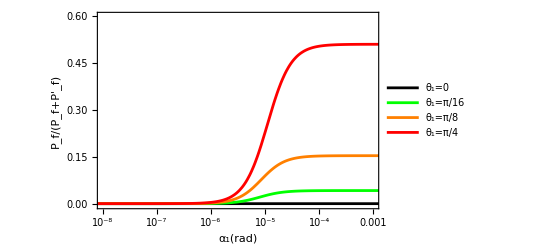

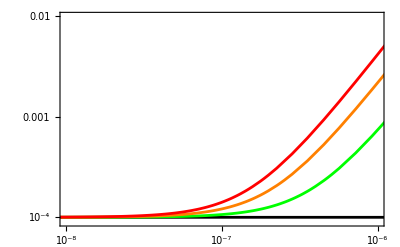

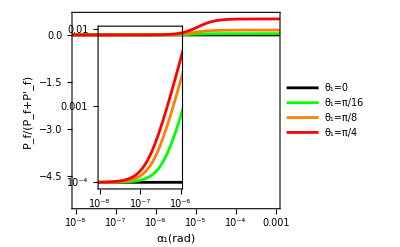

```mathematica
Avsa1=LogLinearPlot[{A[1064.,2α1,10^5,10.64,α1,α1,0,0,0.01],A[1064.,2α1,10^5,10.64,α1,α1,π/16,π/16,0.01],A[1064.,2α1,10^5,10.64,α1,α1,π/8,π/8,0.01],A[1064.,2α1,10^5,10.64,α1,α1,π/4,π/4,0.01]},{α1,10^-9,10^-2},PlotRange->{{10^-8,10^-3},{-0.004,0.6}},PlotStyle->{Black,Green,Orange,Red},PlotLegends->Placed[LineLegend[{Style["θ_1=0",FontSize->10,FontFamily->"TeX"],Style["θ_1=π/16",FontSize->10,FontFamily->"TeX"],Style["θ_1=π/8",FontSize->10,FontFamily->"TeX"],Style["θ_1=π/4",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Left,Bottom}],Frame->True,FrameLabel->{Row[{Style["α_1",FontFamily->"TeX"],Style["(rad)",FontFamily->"Times"]}],Style["P_f/(P_f+P'_f)",FontSlant->"Italic",FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Automatic,None},{Table[{10^n,Superscript[10,n]},{n,-8,0}],None}},TicksStyle->{FontFamily->"TeX"}] 

Avsa1small=LogLogPlot[{A[1064.,2α1,10^5,10.64,α1,α1,0,0,0.01],A[1064.,2α1,10^5,10.64,α1,α1,π/16,π/16,0.01],A[1064.,2α1,10^5,10.64,α1,α1,π/8,π/8,0.01],A[1064.,2α1,10^5,10.64,α1,α1,π/4,π/4,0.01]},{α1,10^-9,10^-4},PlotRange->{{10^-8,10^-6},{0.9 10^-4,10^-2}},PlotStyle->{Black,Green,Orange,Red},Frame->True,LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-4,-2}],None},{Table[{10^n,Superscript[10,n]},{n,-8,-6}],None}},TicksStyle->{FontFamily->"TeX"}] 

Show[Avsa1,Graphics[{Inset[Avsa1small,{-18.05,0.58},{Left,Top},{6.0,6.0}]}]]
```

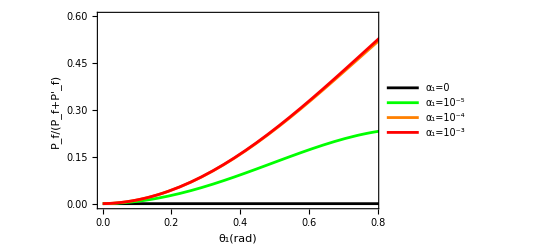

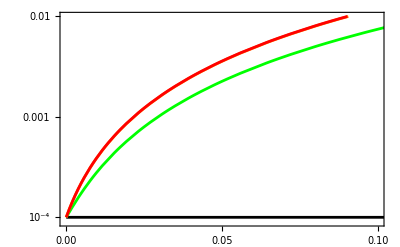

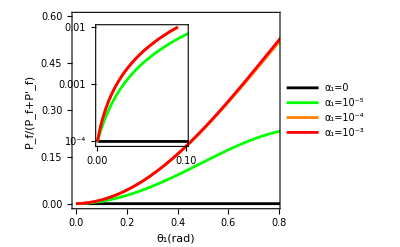

```mathematica
Avsth1=Plot[{A[1064.,0,10^5,10.64,0,0,θ1,θ1,0.01],A[1064.,2 10^-5,10^5,10.64,10^-5,10^-5,θ1,θ1,0.01],A[1064.,2 10^-4,10^5,10.64,10^-4,10^-4,θ1,θ1,0.01],A[1064.,2 10^-3,10^5,10.64,10^-3,10^-3,θ1,θ1,0.01]},{θ1,0,π/2},PlotRange->{{0,3.15/4},{-0.004,0.6}},PlotStyle->{Black,Green,Orange,Red},PlotLegends->Placed[LineLegend[{Style["α_1=0",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-5",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-4",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-3",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Left,Bottom}],Frame->True,FrameLabel->{Row[{Style["θ_1",FontFamily->"TeX"],Style["(rad)",FontFamily->"Times"]}],Style["P_f/(P_f+P'_f)",FontSlant->"Italic",FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Automatic,None},{Automatic,None}},TicksStyle->{FontFamily->"TeX"} ]

Avsth1small=LogPlot[{A[1064.,0,10^5,10.64,0,0,θ1,θ1,0.01],A[1064.,2 10^-5,10^5,10.64,10^-5,10^-5,θ1,θ1,0.01],A[1064.,2 10^-4,10^5,10.64,10^-4,10^-4,θ1,θ1,0.01],A[1064.,2 10^-3,10^5,10.64,10^-3,10^-3,θ1,θ1,0.01]},{θ1,0,π/2},PlotRange->{{0,0.1},{0.9 10^-4,10^-2}},PlotStyle->{Black,Green,Orange,Red},Frame->True,LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-4,-2}],None},{Table[{0.05 n,NumberForm[0.05 n,{2,2}]},{n,0,2}],None}},TicksStyle->{FontFamily->"TeX"} ]

Show[Avsth1,Graphics[{Inset[Avsth1small,{0.01,0.595},{Left,Top},{0.45,0.45}]}]]
```

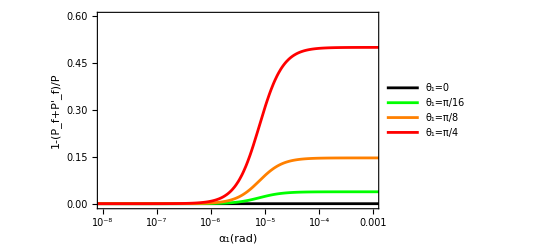

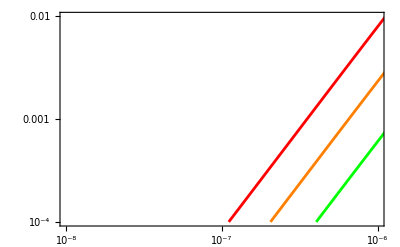

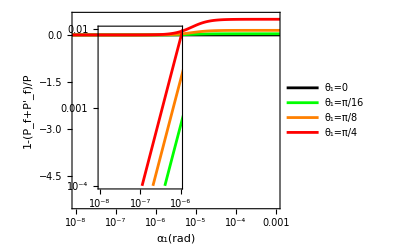

```mathematica
Bvsa1=LogLinearPlot[{B[1064.,2 α1,10^5,10.64,α1,α1,0,0,0.01],B[1064.,2α1,10^5,10.64,α1,α1,π/16,π/16,0.01],B[1064.,2α1,10^5,10.64,α1,α1,π/8,π/8,0.01],B[1064.,2α1,10^5,10.64,α1,α1,π/4,π/4,0.01]},{α1,10^-9,10^-2},PlotRange->{{10^-8,10^-3},{-0.004,0.6}},PlotStyle->{Black,Green,Orange,Red},PlotLegends->Placed[LineLegend[{Style["θ_1=0",FontSize->10,FontFamily->"TeX"],Style["θ_1=π/16",FontSize->10,FontFamily->"TeX"],Style["θ_1=π/8",FontSize->10,FontFamily->"TeX"],Style["θ_1=π/4",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Left,Bottom}],Frame->True,FrameLabel->{Row[{Style["α_1",FontFamily->"TeX"],Style["(rad)",FontFamily->"Times"]}],Style["1-(P_f+P'_f)/P",FontSlant->"Italic",FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Automatic,None},{Table[{10^n,Superscript[10,n]},{n,-8,0}],None}},TicksStyle->{FontFamily->"TeX"}] 

Bvsa1small=LogLogPlot[{B[1064.,2α1,10^5,10.64,α1,α1,0,0,0.01],B[1064.,2α1,10^5,10.64,α1,α1,π/16,π/16,0.01],B[1064.,2α1,10^5,10.64,α1,α1,π/8,π/8,0.01],B[1064.,2α1,10^5,10.64,α1,α1,π/4,π/4,0.01]},{α1,10^-9,10^-4},PlotRange->{{10^-8,10^-6},{10^-4,10^-2}},PlotStyle->{Black,Green,Orange,Red},Frame->True,LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^n,Superscript[10, n]},{n,-4,-2}],None},{Table[{10^n,Superscript[10,n]},{n,-8,-6}],None}},TicksStyle->{FontFamily->"TeX"}] 

Show[Bvsa1,Graphics[{Inset[Bvsa1small,{-18.05,0.58},{Left,Top},{6.0,6.0}]}]]
```

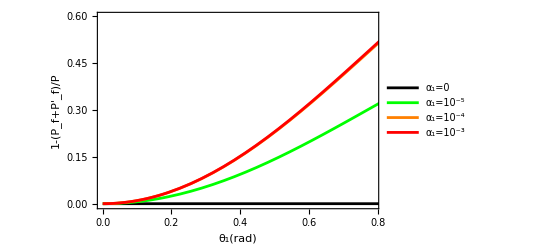

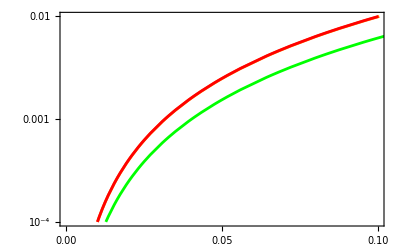

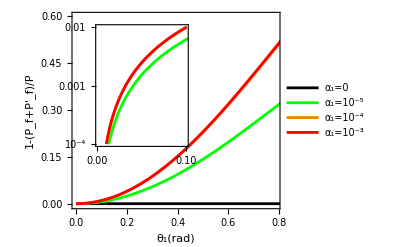

```mathematica
Bvsth1=Plot[{B[1064.,0,10^5,10.64,0,0,θ1,θ1,0.01],B[1064.,2 10^-5,10^5,10.64,10^-5,10^-5,θ1,θ1,0.01],B[1064.,2 10^-4,10^5,10.64,10^-4,10^-4,θ1,θ1,0.01],B[1064.,2 10^-3,10^5,10.64,10^-3,10^-3,θ1,θ1,0.01]},{θ1,0,π/2},PlotRange->{{0,3.15/4},{-0.004,0.6}},PlotStyle->{Black,Green,Orange,Red},PlotLegends->Placed[LineLegend[{Style["α_1=0",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-5",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-4",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-3",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Left,Bottom}],Frame->True,FrameLabel->{Row[{Style["θ_1",FontFamily->"TeX"],Style["(rad)",FontFamily->"Times"]}],Style["1-(P_f+P'_f)/P",FontSlant->"Italic",FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Automatic,None},{Automatic,None}},TicksStyle->{FontFamily->"TeX"} ]

Bvsth1small=LogPlot[{B[1064.,0,10^5,10.64,0,0,θ1,θ1,0.01],B[1064.,2 10^-5,10^5,10.64,10^-5,10^-5,θ1,θ1,0.01],B[1064.,2 10^-4,10^5,10.64,10^-4,10^-4,θ1,θ1,0.01],B[1064.,2 10^-3,10^5,10.64,10^-3,10^-3,θ1,θ1,0.01]},{θ1,0,π/2},PlotRange->{{0,0.1},{10^-4,10^-2}},PlotStyle->{Black,Green,Orange,Red},Frame->True,LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-4,-2}],None},{Table[{0.05 n,NumberForm[0.05n,{2,2}]},{n,0,2}],None}},TicksStyle->{FontFamily->"TeX"} ]

Show[Bvsth1,Graphics[{Inset[Bvsth1small,{0.01,0.595},{Left,Top},{0.45,0.45}]}]]
```

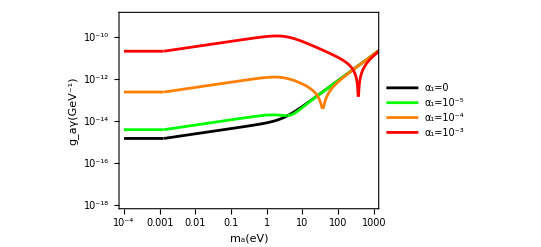

```mathematica
LogLogPlot[{f[m,1064.,0,10^5,10.64,0,0,0,0,0.01,100.,365.],f[m,1064.,2 10^-5,10^5,10.64,10^-5,10^-5,0,0,0.01,100.,365.],f[m,1064.,2 10^-4,10^5,10.64,10^-4,10^-4,0,0,0.01,100.,365.],f[m,1064.,2 10^-3,10^5,10.64,10^-3,10^-3,0,0,0.01,100.,365.]},{m,10^-4,10^6},PlotRange-> {{10^-4,10^3},{10^-18,10^-9}},PlotStyle->{Black,Green,Orange,Red},PlotLegends->Placed[LineLegend[{Style["α_1=0",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-5",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-4",FontSize->10,FontFamily->"TeX"],Style["α_1=10^-3",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Right,Bottom}],Frame->True,FrameLabel->{Style[Row[{Style["m_a",FontSlant->"Italic"],"(eV)"}],FontFamily->"Times"],Style[Row[{Style["g_aγ",FontSlant->"Italic"],"(GeV^-1)"}],FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^i,If[Mod[i,3]==0,Superscript[10,i],""]},{i,-18,-9}],None},{Table[{10^i,Superscript[10,i-13]},{i,-4,3}],None}},TicksStyle->{FontFamily->"TeX"}]
```

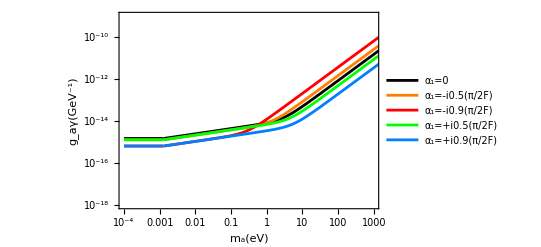

```mathematica
LogLogPlot[{f[m,1064.,0,10^5,10.64,0,0,0,0,0.01,100.,365.],f[m,1064.,0,10^5,10.64,-I 0.5 π/(2 10^5),-I 0.5 π/(2 10^5),0,0,0.01,100.,365.],f[m,1064.,0,10^5,10.64,-I 0.9 π/(2 10^5),-I 0.9 π/(2 10^5),0,0,0.01,100.,365.],f[m,1064.,0,10^5,10.64,I 0.5 π/(2 10^5),I 0.5 π/(2 10^5),0,0,0.01,100.,365.],f[m,1064.,0,10^5,10.64,I 0.9 π/(2 10^5),I 0.9 π/(2 10^5),0,0,0.01,100.,365.]},{m,10^-4,10^6},PlotRange-> {{10^-4,10^3},{10^-18,10^-9}},PlotStyle->{Black,Orange,Red,Green,Blend[{Blue,Cyan},1/2]},PlotLegends->Placed[LineLegend[{Style["α_1=0",FontSize->10,FontFamily->"TeX"],Style["α_1=-i0.5(π/2F)",FontSize->10,FontFamily->"TeX"],Style["α_1=-i0.9(π/2F)",FontSize->10,FontFamily->"TeX"],Style["α_1=+i0.5(π/2F)",FontSize->10,FontFamily->"TeX"],Style["α_1=+i0.9(π/2F)",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Left,Top}],Frame->True,FrameLabel->{Style[Row[{Style["m_a",FontSlant->"Italic"],"(eV)"}],FontFamily->"Times"],Style[Row[{Style["g_aγ",FontSlant->"Italic"],"(GeV^-1)"}],FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^i,If[Mod[i,3]==0,Superscript[10,i],""]},{i,-18,-9}],None},{Table[{10^i,Superscript[10,i-13]},{i,-4,3}],None}},TicksStyle->{FontFamily->"TeX"}]
```

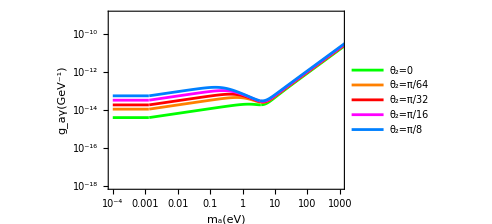

```mathematica
LogLogPlot[{f[m,1064.,α[10^-5,10^-5,0,0],10^5,10.64,10^-5,10^-5,0,0,0.01,100.,365.],f[m,1064.,α[10^-5,10^-5,0,π/64],10^5,10.64,10^-5,10^-5,0,π/64,0.01,100.,365.],f[m,1064.,α[10^-5,10^-5,0,π/32],10^5,10.64,10^-5,10^-5,0,π/32,0.01,100.,365.],f[m,1064.,α[10^-5,10^-5,0,π/16],10^5,10.64,10^-5,10^-5,0,π/16,0.01,100.,365.],f[m,1064.,α[10^-5,10^-5,0,π/8],10^5,10.64,10^-5,10^-5,0,π/8,0.01,100.,365.]},{m,10^-4,10^6},PlotRange-> {{10^-4,10^3},{10^-18,10^-9}},PlotStyle->{Green,Orange,Red, Magenta, Blend[{Blue,Cyan},1/2]},PlotLegends->Placed[LineLegend[{Style["θ_2=0",FontSize->10,FontFamily->"TeX"],Style["θ_2=π/64",FontSize->10,FontFamily->"TeX"],Style["θ_2=π/32",FontSize->10,FontFamily->"TeX"],Style["θ_2=π/16",FontSize->10,FontFamily->"TeX"],Style["θ_2=π/8",FontSize->10,FontFamily->"TeX"]},LegendMarkerSize->{20,10}],{Right,Bottom}],Frame->True,FrameLabel->{Style[Row[{Style["m_a",FontSlant->"Italic"],"(eV)"}],FontFamily->"Times"],Style[Row[{Style["g_aγ",FontSlant->"Italic"],"(GeV^-1)"}],FontFamily->"Times"]},LabelStyle->Black,MaxRecursion-> 5,FrameTicks->{{Table[{10^i,If[Mod[i,3]==0,Superscript[10,i],""]},{i,-18,-9}],None},{Table[{10^i,Superscript[10,i-13]},{i,-4,3}],None}},TicksStyle->{FontFamily->"TeX"}]
```

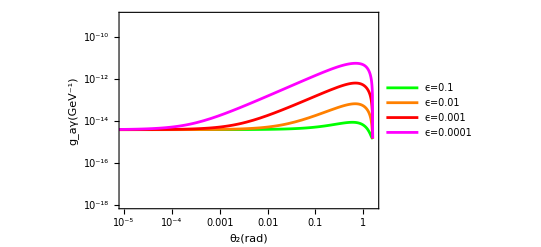

```mathematica
LogLogPlot[{f[10^-3,1064.,α[10^-5,10^-5,0,θ2] ,10^5,10.64,10^-5,10^-5,0,θ2,0.1,100.,365.],f[10^-3,1064.,α[10^-5,10^-5,0,θ2],10^5,10.64,10^-5,10^-5,0,θ2,0.01,100.,365.],f[10^-3,1064.,α[10^-5,10^-5,0,θ2],10^5,10.64,10^-5,10^-5,0,θ2,0.001,100.,365.],f[10^-3,1064.,α[10^-5,10^-5,0,θ2],10^5,10.64,10^-5,10^-5,0,θ2,0.0001,100.,365.]},{θ2,10^-7,π/2},PlotRange-> {{10^-5,3.3/2},{10^-18,10^-9}},PlotLegends->Placed[{Style[ "ϵ=0.1",FontSize->10,FontFamily->"TeX"],Style[ "ϵ=0.01",FontSize->10,FontFamily->"TeX"],Style[ "ϵ=0.001",FontSize->10,FontFamily->"TeX"],Style[ "ϵ=0.0001",FontSize->10,FontFamily->"TeX"]},{Left,Top}] ,PlotStyle->{Green,Orange,Red,Magenta},Frame->True,FrameStyle->Black,FrameLabel->{Row[{Style["θ_2",FontFamily->"TeX"],Style["(rad)",FontFamily->"Times"]}],Style[Row[{Style["g_aγ",FontSlant->"Italic"],"(GeV^-1)"}],FontFamily->"Times"]},MaxRecursion-> 5,FrameTicks->{{Table[{10^i,If[Mod[i,3]==0,Superscript[10,i],""]},{i,-18,-9}],None},{Table[{10^i,Superscript[10,i]},{i,-5,0}],None}},TicksStyle->{FontFamily->"TeX"}]
```